```mathematica
Needs["NDSolve`FEM`"]
```

## Circular integration test with better boundaries

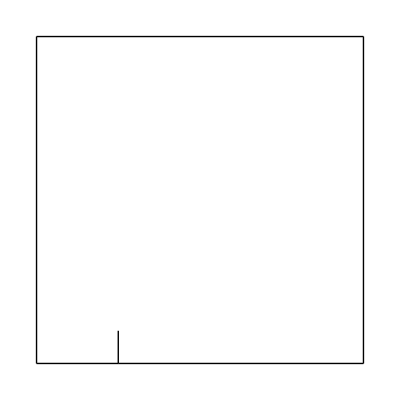

```mathematica
boundary = ToBoundaryMesh[
"Coordinates"->{
{0,0},
{0.25,0},
{0.25,0.1},
{1,0},
{1,1},
{0,1}
},
"BoundaryElements"->{
LineElement[{
{1,2},
{2,3},
{2,4},
{4,5},
{5,6},
{6,1}},
{2,2,2,2,2,2}
]
}
];
reg = ToElementMesh[boundary,
"MeshQualityGoal"->0.7, 
"MaxCellMeasure"->{"Area"->0.01},
MeshRefinementFunction->Function[{vertices,area},(area ≥0.00001Norm[{0.25,0.1}-Mean[vertices]])]
];
boundary["Wireframe"]
```

```mathematica
sol=NDSolveValue[
{
Laplacian[u[x,y],{x,y}]+1==0,
{DirichletCondition[u[x,y]==0,x≤0||x≥1||y≤0||y≥0],
DirichletCondition[u[x,y]==0,x==0.25&&y≥0&&y≤0.1]}
},
u,
{x,y}∈reg,
AccuracyGoal->25,PrecisionGoal->25];
```

```mathematica
Show[
ContourPlot[sol[x,y],{x,y}∈reg],
Graphics[{
Red, Circle[{0.25,0.1},0.1], 
White, Point[{0.25,0.1}]}]
]
```

-Graphics-

#### Now we will integrate in circle

```mathematica
DiskIntegr=NIntegrate[sol[x,y],{x,y}∈Disk[{0.25,0.1},0.1],AccuracyGoal->20,PrecisionGoal->15, MaxRecursion->45];
RealDigits[DiskIntegr]
Print[DiskIntegr]
```

{{4,6,1,1,3,8,2,3,4,4,4,6,5,3,6,3},-3}

0.000461138

#### Whole region

```mathematica
wholeRigIntegr=NIntegrate[sol[x,y],{x,y}∈reg,AccuracyGoal->20,PrecisionGoal->7,MaxRecursion->45];
RealDigits[wholeRigIntegr]
Print[wholeRigIntegr]
```

{{3,4,2,0,2,0,2,3,6,0,8,5,7,1,0,2},-1}

0.034202

#### Max Value of function

```mathematica
maxval=NMaxValue[sol[x,y],{x,y}∈reg]//Quiet;
RealDigits[maxval]
Print[maxval]
```

{{7,2,5,7,9,2,1,8,3,4,6,0,3,5,5,1},-1}

0.0725792

## Test of Mathematica solution itself

```mathematica
CoordinateTransform["Cartesian"->"Polar",{x,y}]
```

{√(x^2+y^2),ArcTan[x,y]}

```mathematica
rmin=0.0000000001;rmax=0.01;
```

```mathematica
region = DiscretizeRegion[ImplicitRegion[√((x-0.25)^2+(y-0.1)^2)≤rmax &&√((x-0.25)^2+(y-0.1)^2)>=rmin,{x,y}],{{0,1},{0,1}},
MaxCellMeasure->0.0000001];
```

```mathematica
func[dx_,dy_]:=1/(Pi(rmax-rmin) √(dx^2+dy^2))Cos[1/2 (-ArcTan[dx,dy]+Pi/2)]
```

### A1 series param evaluation

```mathematica
a1valtest = NIntegrate[func[x-0.25,y-0.1]sol[x,y],{x,y}∈region]
RealDigits[a1valtest]
```

0.0056523

{{5,6,5,2,2,9,7,0,0,8,6,7,6,1,1,2},-2}

## Test With exact implementation like in FreeFem++

```mathematica
BaseVector[nf_Integer, zf_Complex]:=If[Mod[nf,2]==0,-Im[zf^(nf/2.)],Re[zf^(nf/2.)]]
```

### predefined integral

```mathematica
R = 0.01(*same radius is in freefem*);
exponant = 2(*value from FreeFem*);
tipangle = Pi/2;
x0 = 0.25;
y0 = 0.1;
```

```mathematica
int2d[sol_] := NIntegrate[
sol, 
{x,y}∈Disk[{0.25,0.1},R],
AccuracyGoal->20, PrecisionGoal->8,MaxRecursion->50,WorkingPrecision->15
];
```

```mathematica
a[order_Integer]:=
NIntegrate[
sol[x,y] 
Exp[-((√((x - 0.25)^2+(y - 0.1)^2))/R)^exponant]
BaseVector[order, 
Exp[-I tipangle] (x-x0 + I(y - y0)) 
],
{x,y}∈Disk[{x0,y0},R],
AccuracyGoal->10, 
PrecisionGoal->8,
MaxRecursion->50,
WorkingPrecision->15]/
NIntegrate[
Exp[-((√((x - 0.25)^2+(y - 0.1)^2))/R)^exponant]
BaseVector[order, 
Exp[-I tipangle] (x-x0 + I(y - y0)) ]^2,
{x,y}∈Disk[{x0,y0},R],
AccuracyGoal->10, 
PrecisionGoal->8,
MaxRecursion->50,
WorkingPrecision->15]
```

### And final value check!

```mathematica
a[1]
```

0.10211079158797

```mathematica
a[2]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.00001651372651338-0.000016513727098827 ⅈ

```mathematica
a[3]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

7.2392604387979×10^-7-1.4478544251383×10^-6 ⅈ

```mathematica
BaseVector[2,1+I]
```

-1.